```mathematica
(*collaborator: Hongshuo Wang, Qian Liu*)
```

```mathematica
pivot[iStar_, jStar_, tableau_] := (
newTableau = tableau;
numberRows = Dimensions[tableau][[1]];
numberCols = Dimensions[tableau][[2]];
(* switch row tableau variables *)
newTableau[[1,jStar]] = tableau[[iStar, numberCols]];
newTableau[[iStar, numberCols]] = tableau[[1,jStar]];
(* switch column tableau variables *)
newTableau[[numberRows,jStar]] = -tableau[[iStar, 1]];
newTableau[[iStar, 1]] = -tableau[[numberRows,jStar]];
(* adjust loop bounds to skip 1st column and last row *)
For[i = 2, i < numberRows, i++,
For[j=2,j<numberCols,j++,
If[i == iStar && j == jStar, 
newTableau[[i,j]]=1/tableau[[iStar, jStar]]];
If[i== iStar && j ≠ jStar,
newTableau[[i, j]]= -tableau[[iStar, j]]/tableau[[iStar, jStar]]];
If[i ≠ iStar && j == jStar,
newTableau[[i, j]]= tableau[[i, jStar]]/tableau[[iStar, jStar]]];
If[i ≠ iStar && j ≠ jStar,
newTableau[[i, j]] = tableau[[i, j]]-tableau[[iStar, j]]*tableau[[i, jStar]]/tableau[[iStar,jStar]]];
]
];
Return[newTableau];
)

(* max z(x,y)=17x+11y-9
Subject to
g1(x1,x2)= 2x1 + x2 ≤ 32 = b1
g2(x1,x2)= x1 + x2 ≤ 20 = b2
g3(x1,x2)=x1+ 2x2 ≤38 = b3
x≥0
*)

(*1.*)
Clear[x1,x2]
z[x1_,x2_]:=17x1+11x2;
g1[x1_,x2_]:=2x1+x2;
g2[x1_,x2_]:=x1+x2;
g3[x1_,x2_]:=x1+2x2;
g1[x1_]:=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]];
g2[x1_]:=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]];
g3[x1_]:=x2/.Solve[g3[x1,x2]==b3,{x2}][[1,1]];
b1=32;
b2=20;
b3=38;

Plot[{g1[x],g2[x],g3[x]},{x,-10,50},AspectRatio->Automatic,PlotRange->{-10,50},PlotLegends -> "Expressions"]
```

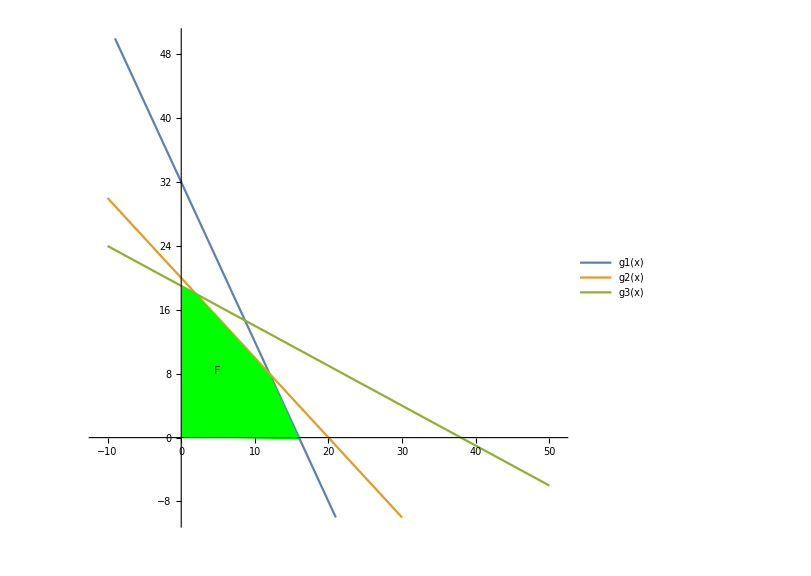

```mathematica
u=x1/.Solve[g2[x1,x2]==20&&x2==0][[1,1]];
v=x2/.Solve[g2[x1,x2]==20&&x2==0][[1,2]];
b1_max = g1[u,v]
```

40

```mathematica
u=x1/.Solve[g2[x1,x2]==20&&g3[x1,x2]==38][[1,1]];
v=x2/.Solve[g2[x1,x2]==20&&g3[x1,x2]==38][[1,2]];
b1_min = g1[u,v]
```

22

```mathematica
u=x1/.Solve[g1[x1,x2]==32&&g3[x1,x2]==38][[1,1]];
v=x2/.Solve[g1[x1,x2]==32&&g3[x1,x2]==38][[1,2]];
b2_max = g2[u,v]
```

70/3

```mathematica
u=x1/.Solve[g3[x1,x2]==38&&x1==0][[1,1]];
v=x2/.Solve[g3[x1,x2]==38&&x1==0][[1,2]];
b2_min = g2[u,v]
```

19

```mathematica
u=x1/.Solve[g2[x1,x2]==20&&x1==0][[1,1]];
v=x2/.Solve[g2[x1,x2]==20&&x1==0][[1,2]];
b3_max = g3[u,v]
```

40

```mathematica
u=x1/.Solve[g1[x1,x2]==32&&g2[x1,x2]==20][[1,1]];
v=x2/.Solve[g1[x1,x2]==32&&g2[x1,x2]==20][[1,2]];
b3_min = g3[u,v]
```

28

```mathematica
(* 
	b1: min =22; max = 40;
	b2: min =19; max = 70/3;
	b3: min =28; max = 40;
*)
```

```mathematica
(*3.

	a) db=(0 2 0)
b) db=(3 0 0)
c) db=(3 2 0)
d) db=(3-2 0)
*)
```

```mathematica
db1=0;
db2=0;
db3=0;
m0={" ","x1","x2",1," "};
m1={"y1",-2,-1,(b1+db1),"s1"}; (* baseline b1 = 32 (db1=0) *)
m2={"y2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=0) *)
m3={"y3",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["baseline initial = ",MatrixForm[a]];
```

baseline initial = (  | x1 | x2 | 1 |  
y1 | -2 | -1 | 32 | s1
y2 | -1 | -1 | 20 | s2
y3 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s1 | x2 | 1 |  
v1 | -1/2 | -1/2 | 16 | x1
y2 | 1/2 | -1/2 | 4 | s2
y3 | 1/2 | -3/2 | 22 | s3
-1 | 17/2 | -5/2 | -263 | -z→min
 | -y1 | -v2 | w→max | )

```mathematica
c=pivot[3,3,b];
Print["c = ",MatrixForm[c]];
```

c = (  | s1 | s2 | 1 |  
v1 | -1 | 1 | 12 | x1
v2 | 1 | -2 | 8 | x2
y3 | -1 | 3 | 10 | s3
-1 | 6 | 5 | -283 | -z→min
 | -y1 | -y2 | w→max | )

```mathematica
(* primary basic solution *)
xStarBase={12,8};
zStarBase=283;
yStar={6,5,0};
wStar=283;
y1 = yStar[[1]];
y2 = yStar[[2]];
y3 = yStar[[3]];
m0={" ","y1","y2","y3 "," "};
m1={"x1",-2,-1,(b1+db1),"s1"}; (* baseline b1 = 32 (db1=0) *)
m2={"x2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=0) *)
m3={"-1",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["baseline initial = ",MatrixForm[a]];
```

baseline initial = (  | y1 | y2 | y3  |  
x1 | -2 | -1 | 32 | s1
x2 | -1 | -1 | 20 | s2
-1 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
m0={"","y1","y2","y3",1,""};
m1={"x1",2,1,1,-17,"v1"};
m2={"x2",1,1,2,-11,"v2"};
mobj={-1,32,20,38,-9,"w→max"};
mbottom={"",-"s1",-"s2",-"s3","-z→min",""};
aaa={m0,m1,m2,mobj,mbottom};
MatrixForm[aaa]
```

( | y1 | y2 | y3 | 1 | 
x1 | 2 | 1 | 1 | -17 | v1
x2 | 1 | 1 | 2 | -11 | v2
-1 | 32 | 20 | 38 | -9 | w→max
 | -s1 | -s2 | -s3 | -z→min | )

```mathematica
d=pivot[2,2,aaa];
Print["d = ",MatrixForm[d]];
```

d = ( | v1 | y2 | y3 | 1 | 
s1 | 1/2 | -1/2 | -1/2 | 17/2 | y1
x2 | 1/2 | 1/2 | 3/2 | -5/2 | v2
-1 | 16 | 4 | 22 | 263 | w→max
 | -x1 | -s2 | -s3 | -z→min | )

```mathematica
e=pivot[3,3,d];
Print["e = ",MatrixForm[e]];
```

e = ( | v1 | v2 | y3 | 1 | 
s1 | 1 | -1 | 1 | 6 | y1
s2 | -1 | 2 | -3 | 5 | y2
-1 | 12 | 8 | 10 | 283 | w→max
 | -x1 | -x2 | -s3 | -z→min | )

```mathematica
(* row tableau == (column tableau)
	dzStar=delz.dxStar=yStar.db
*)
```

```mathematica
(*4.*)
Clear[z,zStar,b1,b2,b3]

x1Star[b1_,b2_]:=x1/.Solve[g1[x1,x2]==b1&&g2[x1,x2]==b2,{x1,x2}][[1,1]]
x2Star[b1_,b2_]:=x2/.Solve[g1[x1,x2]==b1&&g2[x1,x2]==b2,{x1,x2}][[1,2]]
z[x1_,x2_]:=17x1+11x2-9
zStar[b1_,b2_]:=z[x1Star[b1,b2],x2Star[b1,b2]]
Print["zStar[b1,b2]=",Simplify[zStar[b1,b2]]]
dzdb1=D[zStar[b1,b2],{b1,1}]
dzdb2=D[zStar[b1,b2],{b2,1}]
dzdb3=D[zStar[b1,b2],{b3,1}]
y1==dzdb1
y2==dzdb2
y3==dzdb3
```

zStar[b1,b2]=-9+6 b1+5 b2

6

5

0

True

True

True

```mathematica
(*5.*)
(*
	a) db=(0 2 0)
b) db=(3 0 0)
c) db=(3 2 0)
d) db=(3-2 0)
*)
```

```mathematica
delz={17,11}; 
delg1={2,1};
delg2={1,1};
delg3={1,2};
b1=32;
b2=20;
b3=38;
```

```mathematica
(* a)
```

```mathematica
db1=0;
db2=2;
db3=0;
m0={" ","x1","x2",1," "};
m1={"y1",-2,-1,(b1+db1),"s1"}; (* baseline b1 =  32(db1=0) *)
m2={"y2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=0) *)
m3={"y3",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["db=(0,2,0) initial = ",MatrixForm[a]];
```

db=(0,2,0) initial = (  | x1 | x2 | 1 |  
y1 | -2 | -1 | 32 | s1
y2 | -1 | -1 | 22 | s2
y3 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s1 | x2 | 1 |  
v1 | -1/2 | -1/2 | 16 | x1
y2 | 1/2 | -1/2 | 6 | s2
y3 | 1/2 | -3/2 | 22 | s3
-1 | 17/2 | -5/2 | -263 | -z→min
 | -y1 | -v2 | w→max | )

```mathematica
c=pivot[3,3,b];
Print["db=(0,2,0) optimal = ",MatrixForm[c]];
```

db=(0,2,0) optimal = (  | s1 | s2 | 1 |  
v1 | -1 | 1 | 10 | x1
v2 | 1 | -2 | 12 | x2
y3 | -1 | 3 | 4 | s3
-1 | 6 | 5 | -293 | -z→min
 | -y1 | -y2 | w→max | )

```mathematica
xStarNew ={10,12};
zStarNew=293
dx=xStarNew-xStarBase
dz = zStarNew-zStarBase
dz==delz.dx==(y1 delg1+y2 delg2+y3 delg3).dx==y1(delg1.dx)+y2(delg2.dx)+y3(delg3.dx)==y1 db1+y2 db2+y3 db3
```

293

{-2,4}

10

True

```mathematica
(*b.*)
```

```mathematica
db1=3;
db2=0;
db3=0;
m0={" ","x1","x2",1," "};
m1={"y1",-2,-1,(b1+db1),"s1"}; (* baseline b1 =  32(db1=0) *)
m2={"y2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=0) *)
m3={"y3",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["db=(3,0,0) initial = ",MatrixForm[a]];
```

db=(3,0,0) initial = (  | x1 | x2 | 1 |  
y1 | -2 | -1 | 35 | s1
y2 | -1 | -1 | 20 | s2
y3 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s1 | x2 | 1 |  
v1 | -1/2 | -1/2 | 35/2 | x1
y2 | 1/2 | -1/2 | 5/2 | s2
y3 | 1/2 | -3/2 | 41/2 | s3
-1 | 17/2 | -5/2 | -577/2 | -z→min
 | -y1 | -v2 | w→max | )

```mathematica
c=pivot[3,3,b];
Print["db=(3,0,0) optimal = ",MatrixForm[c]];
```

db=(3,0,0) optimal = (  | s1 | s2 | 1 |  
v1 | -1 | 1 | 15 | x1
v2 | 1 | -2 | 5 | x2
y3 | -1 | 3 | 13 | s3
-1 | 6 | 5 | -301 | -z→min
 | -y1 | -y2 | w→max | )

```mathematica
xStarNew ={15,5};
zStarNew=301
dx=xStarNew-xStarBase
dz = zStarNew-zStarBase
dz==delz.dx==(y1 delg1+y2 delg2+y3 delg3).dx==y1(delg1.dx)+y2(delg2.dx)+y3(delg3.dx)==y1 db1+y2 db2+y3 db3
```

301

{3,-3}

18

True

```mathematica
(*c.*)
```

```mathematica
db1=3;
db2=2;
db3=0;
m0={" ","x1","x2",1," "};
m1={"y1",-2,-1,(b1+db1),"s1"}; (* baseline b1 =  32(db1=0) *)
m2={"y2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=0) *)
m3={"y3",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["db=(3,2,0) initial = ",MatrixForm[a]];
```

db=(3,2,0) initial = (  | x1 | x2 | 1 |  
y1 | -2 | -1 | 35 | s1
y2 | -1 | -1 | 22 | s2
y3 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s1 | x2 | 1 |  
v1 | -1/2 | -1/2 | 35/2 | x1
y2 | 1/2 | -1/2 | 9/2 | s2
y3 | 1/2 | -3/2 | 41/2 | s3
-1 | 17/2 | -5/2 | -577/2 | -z→min
 | -y1 | -v2 | w→max | )

```mathematica
c=pivot[3,3,b];
Print["db=(3,2,0) optimal = ",MatrixForm[c]];
```

db=(3,2,0) optimal = (  | s1 | s2 | 1 |  
v1 | -1 | 1 | 13 | x1
v2 | 1 | -2 | 9 | x2
y3 | -1 | 3 | 7 | s3
-1 | 6 | 5 | -311 | -z→min
 | -y1 | -y2 | w→max | )

```mathematica
xStarNew ={13,9};
zStarNew=311
dx=xStarNew-xStarBase
dz = zStarNew-zStarBase
dz==delz.dx==(y1 delg1+y2 delg2+y3 delg3).dx==y1(delg1.dx)+y2(delg2.dx)+y3(delg3.dx)==y1 db1+y2 db2+y3 db3
```

311

{1,1}

28

True

```mathematica
(*d.*)
```

```mathematica
db1=3;
db2=-2;
db3=0;
m0={" ","x1","x2",1," "};
m1={"y1",-2,-1,(b1+db1),"s1"}; (* baseline b1 =  32(db1=0) *)
m2={"y2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=0) *)
m3={"y3",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["db=(3,-2,0) initial = ",MatrixForm[a]];
```

db=(3,-2,0) initial = (  | x1 | x2 | 1 |  
y1 | -2 | -1 | 35 | s1
y2 | -1 | -1 | 18 | s2
y3 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s1 | x2 | 1 |  
v1 | -1/2 | -1/2 | 35/2 | x1
y2 | 1/2 | -1/2 | 1/2 | s2
y3 | 1/2 | -3/2 | 41/2 | s3
-1 | 17/2 | -5/2 | -577/2 | -z→min
 | -y1 | -v2 | w→max | )

```mathematica
c=pivot[3,3,b];
Print["db=(3,-2,0) optimal = ",MatrixForm[c]];
```

db=(3,-2,0) optimal = (  | s1 | s2 | 1 |  
v1 | -1 | 1 | 17 | x1
v2 | 1 | -2 | 1 | x2
y3 | -1 | 3 | 19 | s3
-1 | 6 | 5 | -291 | -z→min
 | -y1 | -y2 | w→max | )

```mathematica
xStarNew ={17,1};
zStarNew=291
dx=xStarNew-xStarBase
dz = zStarNew-zStarBase
dz==delz.dx==(y1 delg1+y2 delg2+y3 delg3).dx==y1(delg1.dx)+y2(delg2.dx)+y3(delg3.dx)==y1 db1+y2 db2+y3 db3
```

291

{5,-7}

8

True